#### Esercitazione Parte 1 - ArcTan

```mathematica
Clear["Global`*"]
```

```mathematica
y = 1
```

1

```mathematica
x = 10
```

10

```mathematica
ArcTan[y/x]
```

ArcTan[1/10]

```mathematica
N[ArcTan[y/x]] (*angolo in radianti*)
```

0.0996687

```mathematica
N[ArcTan[y/x]*180/Pi]
```

5.71059

```mathematica
N[ArcTan[x,y]]*180/Pi
```

5.71059

```mathematica
y = -1
```

-1

```mathematica
x = -10
```

-10

```mathematica
N[ArcTan[y/x]*180/Pi]
```

5.71059

```mathematica
N[ArcTan[x,y]]*180/Pi (*arctan a due argomenti*)
```

-174.289

#### Parte 2 - Manipulate di una Manovella

```mathematica
Clear["Global`*"]
```

```mathematica
x + 10
```

10+x

```mathematica
Manipulate[x+10,{x,0,1}]
```

#### Manovella inclinata di 10 gradi

```mathematica
l2 = 1
```

1

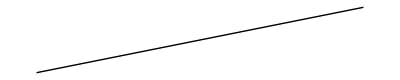

```mathematica
Graphics[
	Line[
	{{0,0},{l2 Cos[10/180*Pi],
	l2 Sin[10/180*Pi]}}]]
```

```mathematica
Show[
Graphics[
	Line[
	{{0,0},{l2 Cos[10/180*Pi],
	l2 Sin[10/180*Pi]}}]],
PlotRange->{{-2,2},{-2,2}}
] (*il range è -2,2 sia su x che y*)
```

-Graphics-

```mathematica
Manipulate[
Show[
Graphics[
	Line[
	{{0,0},{l2 Cos[th2*Pi],
	l2 Sin[th2]}}/.th2->th22]],
PlotRange->{{-2,2},{-2,2}}
],{th22,0,1}
]
```

#### Analisi di posizione

```mathematica
Clear["Global`*"]
```

```mathematica
l2 = 0.17;
l3 = 0.77;
l4 = 0.75;
l5 = 0.59;
```

```mathematica
l = 0.70;
h = 80;
```

```mathematica
Cx = l2 Cos[th2] - l
```

-0.7+0.17 Cos[th2]

```mathematica
Cy = l2 Sin[th2] - h
```

-80+l2Sin[th2]

```mathematica
A = 2Cx l3
```

1.54 (-0.7+0.17 Cos[th2])

```mathematica
B = 2  Cy l3
```

1.54 (-80+l2Sin[th2])

```mathematica
CC = Cx^2 + Cy^2 + l3^2 -l4^2
```

0.0304+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2

#### disegnamo la config del quadrilatero

```mathematica
th31 = 2 ArcTan[-(B+Sqrt[A^2+B^2-CC^2])/(CC-A)]
```

2 ArcTan[(-√(2.3716 (-0.7+0.17 Cos[th2])^2-(0.0304+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2)^2+2.3716 (-80+l2Sin[th2])^2)-1.54 (-80+l2Sin[th2]))/(0.0304-1.54 (-0.7+0.17 Cos[th2])+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2)]

```mathematica
th41 = ArcTan[(-(Cx+ l3 Cos[th31])),(-(Cy + l3 Cos[th31]))]
```

ArcTan[0.7-0.17 Cos[th2]-0.77 Cos[2 ArcTan[(-√(2.3716 (-0.7+0.17 Cos[th2])^2-(0.0304+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2)^2+2.3716 (-80+l2Sin[th2])^2)-1.54 (-80+l2Sin[th2]))/(0.0304-1.54 (-0.7+0.17 Cos[th2])+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2)]],80-0.77 Cos[2 ArcTan[(-√(2.3716 (-0.7+0.17 Cos[th2])^2-(0.0304+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2)^2+2.3716 (-80+l2Sin[th2])^2)-1.54 (-80+l2Sin[th2]))/(0.0304-1.54 (-0.7+0.17 Cos[th2])+(-0.7+0.17 Cos[th2])^2+(-80+l2Sin[th2])^2)]]-l2Sin[th2]]

```mathematica
Manipulate[
Show[
Graphics[Line[{{0,0},{12 Cos[th2],12 Sin[th2]}}/. th2->th22]],Graphics[Line[{{12 Cos[th2],12 Sin[th2]},{12 Cos[th2]+13 Cos[1],12 Sin[th2]+13 Sin[1]}}]/. th2->th22],Graphics[Line[{{12 Cos[th2]+13 Cos[th31],12 Sin[th2]+13 Sin[th31]},{12 Cos[th2]+13 Cos[th31]+14 Cos[th41],12 Sin[th2]+13 Sin[th31]+14 Sin[th41]}}]]/. th2->th22],
Graphics[Line[{{12 Cos[th2]+13 Cos[th31]+14 Cos[th41],12 Sin[th2]+13 Sin[th31]+14 Sin[th41]},{12 Cos[th2]+13 Cos[th31]+14 Cos[th41]+15 Cos[th41],12 Sin[th2]+13 Sin[th31]+14 Sin[th41]+15 Sin[th41]}}/. th2->th22]],
{th22,0,10 Pi}]
```

Manipulate::vsform: Manipulate argument  does not have the correct form for a variable specification.

Manipulate[Show[-Graphics-,-Graphics-,-Graphics-/.th2→th22],-Graphics-,{th22,0,10 π}]

Show::gcomb: "Could not combine the graphics objects in ."